```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @ Import["test1-add.dat"];
```

```mathematica
len=Length[l]
1./Sqrt[len]
```

65536

0.00390625

```mathematica
Mean[l]
StandardDeviation[l]
```

20.9285

121.337

{1.,0.999964,0.999928,0.999892,0.999856,0.99982,0.999785,0.999749,0.999714,0.999679,0.999644,0.999609,0.999574,0.999539,0.999504,0.999469,0.999433,0.999398,0.999362,0.999326,0.99929}

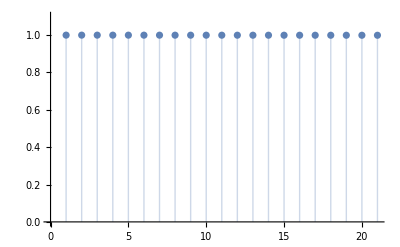

20.9925

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

```mathematica
(* Allan variance estimate *)
diffs=Most[l]-Rest[l];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.500117

0.707189

```mathematica
(* Convert to integers *)
lint=N@Round[l];
Mean[lint]
StandardDeviation[lint]
```

20.9274

121.337

```mathematica
(* Allan variance estimate *)
diffs=Most[lint]-Rest[lint];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.582947

0.76351

{1.,0.999958,0.999922,0.999886,0.99985,0.999814,0.999779,0.999744,0.999709,0.999673,0.999638,0.999603,0.999569,0.999534,0.999499,0.999463,0.999428,0.999393,0.999357,0.999321,0.999285}

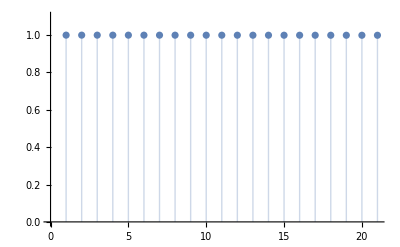

20.9924

```mathematica
cf=CorrelationFunction[N[lint],{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

2.

{a→190.062,x0→-2.17381,σ→155.795}

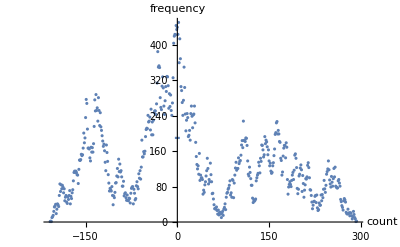

```mathematica
(* Distribution *)
ta=Tally[lint];
x0est=Sort[ta,#1[[2]]>#2[[2]]&][[1,1]]
p1=ListPlot[ta,AxesLabel->{"count","frequency"},LabelStyle->Larger];
fnc=a Exp[-(x-x0)^2/(2σ^2)];
sol=FindFit[ta,fnc,{{a,20000},{x0,x0est},{σ,1}},x]
fnc=fnc/.sol;
p2=Plot[fnc,{x,-4,4},PlotRange->All];
pp=Show[p1,p2]
```

1.00297

{1.,0.00619964,0.00374193,-0.000611778,-0.00255536,-0.00423973,-0.00148864,-0.00502315,0.00734323,-0.00546153,0.000821242,-0.00274852,-0.000578107,-0.000731643,0.00759331,-0.00636492,-0.00305625,0.00358196,-0.00378417,0.000255157,0.00156541}

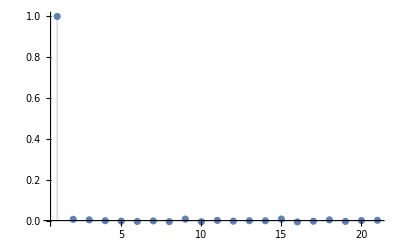

0.994458

```mathematica
(* LSB correlations *)
l2=Map[Mod[#,2]&,l];
Mean[l2]
cf=CorrelationFunction[l2,{20}]
ListPlot[cf,Filling->0,PlotRange->All]
Total[cf]
```